```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/fluctuations_T/PQM/buffer

```mathematica
V=Flatten[Import["./Vtotal.dat"]]*197.33^4;
T=Flatten[Import["./TMeV.dat"]];
mf=Flatten[Import["./mf.dat"]];
p=Transpose[{T/190,-(V-V[[1]])/T^4}];
HotQCDp=Flatten[Import["../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
```

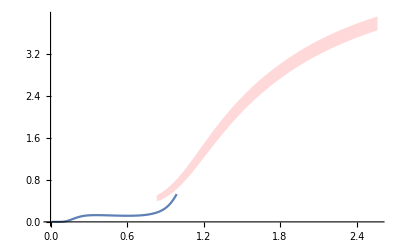

```mathematica
ListLinePlot[{p,Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None}]
```

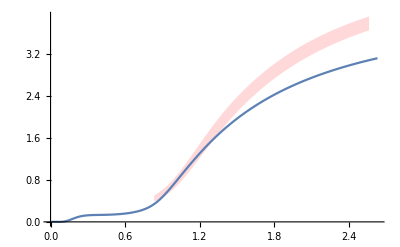

-Graphics-

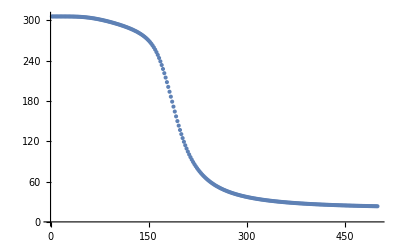

```mathematica
ListPlot[Transpose[{T,mf}]]
```